```mathematica
L=500;(* lattice sites *)
ν=.01;(* filling fraction *)
NF = Floor[ν*L];(* number of particles *)
NF =If[EvenQ[NF],NF+1,NF]
ρ=NF/L;(* average density *)
t=1.0;(* hopping amplitude *) 
usePBC=no; (* PBC yes / no *)
```

5

```mathematica
Ham = ConstantArray[0,{L,L}];
Do[
Ham[[ii,ii+1]]=-t
,{ii,1,L-1}]
If[usePBC,Ham[[1,L]]=-t;]
Ham = Ham + Ham†;
{eval,evec}=Eigensystem[Ham];(* compute the eigensystem *)
order=Ordering[eval];(* bring to ascending order Subscript[E, 1] ≤ Subscript[E, 2] ≤ Subscript[E, 3] ≤ ... *)
eval = eval[[order]];
evec = evec[[order]];
If[DeleteDuplicates[Chop[eval-Diagonal[evec.Ham.evecᵀ],10^-14]][[1]]≠ 0, Print["THIS IS WRONG!"] ](* the transposed eigenvector matrix diagonalizes H *)
gs=evec[[;;NF]];(* modes contributing to the groundstate *)
idx = Join[Table[i,{i,1,NF-1}],{NF+1}]; (* modes contributing to the first excited state *)
fex = evec[[idx]];
obdmGS=gsᵀ.gs;(*the greens function <Subscript[(c†), i] Subscript[c, j]>_GS*)
obdmFEX=fexᵀ.fex;(*the greens function <Subscript[(c†), i] Subscript[c, j]>_(1^st ex.)*)
κinv=ρ^2*( Total[eval[[;;NF+1]]]+Total[eval[[;;NF-1]]]-2*Total[eval[[;;NF]]]) ;(* the inverse compressibility *)
nncorrGS[i_,j_]:=obdmGS[[i,j]]KroneckerDelta[i,j]-obdmGS[[i,j]]*obdmGS[[j,i]]; (* Wick expansion of <Subscript[n, i] Subscript[n, j]>-<Subscript[n, i]><Subscript[n, j]>*)
nncorrFEX[i_,j_]:=obdmFEX[[i,j]]KroneckerDelta[i,j]-obdmFEX[[i,j]]*obdmFEX[[j,i]]; (* Wick expansion of <Subscript[n, i] Subscript[n, j]>-<Subscript[n, i]><Subscript[n, j]>*)
SGS[k_]=1/L*Sum[Exp[ⅈ * k * (x-y)]*nncorrGS[x,y],{x,1,L},{y,1,L}];(* the structure factor *)
SFEX[k_]=1/L*Sum[Exp[ⅈ * k * (x-y)]*nncorrFEX[x,y],{x,1,L},{y,1,L}];(* the structure factor *)
velocity = κinv /π/ρ^2//N; (* formula for the velocity of sound *)
luttingerK = L*S[2π/L];(* the luttinger K from the structure factor *)
Print["luttinger K=", luttingerK]
EFEX=Tr[obdmFEX.Ham];(* energy of the ground state *)
EGS=Tr[obdmGS.Ham];(* energy of the excited state *)
ELS=(EFEX-EGS); (* the level splitting *)
If[!((Tr[obdmGS.Ham])==(eval[[;;NF]]//Total))==((Tr[obdmFEX.Ham])==(eval[[;;NF-1]]//Total)+eval[[NF+1]]),Print["WRONG!"]] (* just a check *)
```

If[no,Ham⟦1,L⟧=-t;]

luttinger K=500 S[π/250]

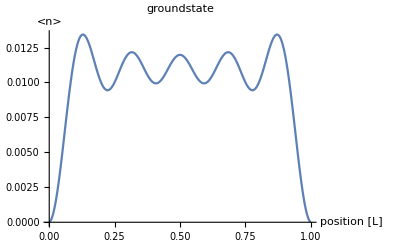

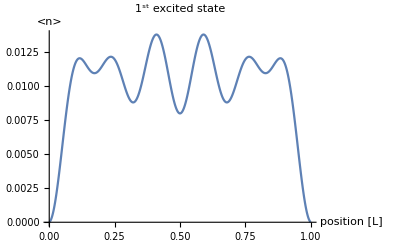

```mathematica
densGS[L]=ListPlot[Diagonal[obdmGS],DataRange->{0,1},Joined->True,AxesLabel->{"position [L]","<n>"},PlotLabel->"groundstate"]
densFEX[L]=ListPlot[Diagonal[obdmFEX],DataRange->{0,1},Joined->True,AxesLabel->{"position [L]","<n>"},PlotLabel->"1^st excited state"]
```

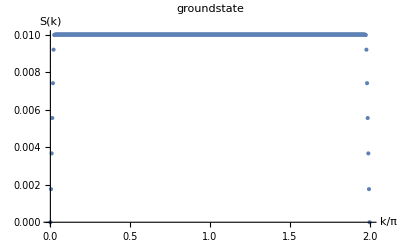

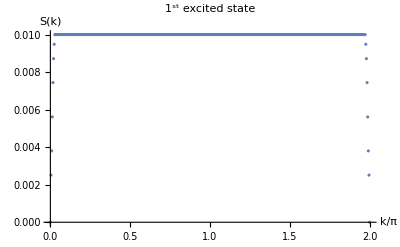

```mathematica
ListPlot[Table[{k/π,SGS[N[k]]},{k,0,2π,2π/L}],PlotRange->Full,AxesLabel->{"k/π","S(k)"},PlotLabel->"groundstate"]
ListPlot[Table[{k/π,SFEX[N[k]]},{k,0,2π,2π/L}],PlotRange->Full,AxesLabel->{"k/π","S(k)"},PlotLabel->"1^st excited state"]
```

```mathematica
ListPlot[{Table[{k/π,k^2/(2SGS[N[k]])},{k,0,16π/L,If[usePBC,2,1]*π/L}],{{If[usePBC,2,1]/L,2ELS}}},PlotStyle->{Automatic,Red},PlotLegends->Placed[{"(ℏk)^2/(2  mS (k))","2(E_1-E_0)"},{Right,Bottom}],PlotRange->Full,AxesLabel->{"k/π[1/a]","energy [ℏ]"}]
```

Table::iterb: Iterator {k,0,(4 π)/125,1/500 π If[no,2,1]} does not have appropriate bounds.

Table::iterb: Iterator {k,0,0.100530964914873,0.00628318530717959 If[no,2.,1.]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListPlot::lpn: {{},{{0.002 If[no,2.,1.],0.000864889}}} is not a list of numbers or pairs of numbers.

ListPlot[{Table[{k/π,k^2/(2 SGS[N[k]])},{k,0,(4 π)/125,1/500 π If[no,2,1]}],{{1/500 If[no,2,1],0.000864889}}},PlotStyle→{Automatic,RGBColor[1, 0, 0]},PlotLegends→Placed[{(ℏk)^2/(2  mS (k)),2(E_1-E_0)},{Right,Bottom}],PlotRange→Full,AxesLabel→{k/π[1/a],energy [ℏ]}]

```mathematica
zero p.b.c.N=2;4;6;
i=+/- 1; +/- 3
i.e. Sin, no 1, no Cos
N=2:
```

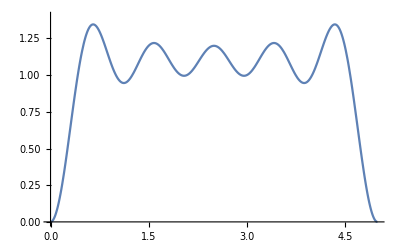

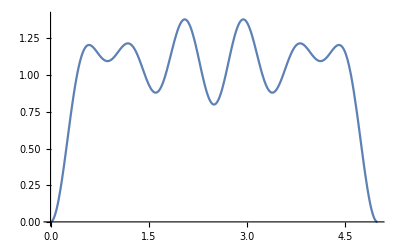

```mathematica
Clear[L];Clear[ρ];k[i_,L_]:=π/L i;(* allowed momenta *)
f[i_,L_,x_]:=(√2)/(√L)Sin[k[i,L]x];(* single-particle states *)
densitygs[N_,x_]:=FullSimplify[∑_(i=1)^N Abs[f[i,N,x]]^2] (*g.s. density *)
densityexc[N_,x_]:=FullSimplify[∑_(i=1)^(N-1) Abs[f[i,N,x]]^2+Abs[f[N+1,N,x]]^2](* density of the first excited state *)
Plot[{densitygs[NF,x]},{x,0,NF},PlotRange->{Automatic,{0,1.4}}]
Plot[{densityexc[NF,x]},{x,0,NF},PlotRange->{Automatic,{0,1.4}}]
```

```mathematica
Egs=ℏ^2/(2m)(∑_(i=1)^N k[i,L]^2) /.L->N/ρ(*g.s. energy *)
Eexc=ℏ^2/(2m)(∑_(i=1)^(N-1) k[i,L]^2+k[N+1,L]^2)/.L->N/ρ//Simplify(* energy of the first excited state *)
```

((1+N) (1+2 N) π^2 ρ^2 ℏ^2)/(12 m N)

((6+13 N+3 N^2+2 N^3) π^2 ρ^2 ℏ^2)/(12 m N^2)

```mathematica
gap=Eexc-Egs//Simplify(* gap energy*)
Series[gap,{N,∞,1}]
vs ℏ k[1,L]/.vs->(π ℏ ρ)/m/.L->N/ρ(* energy of a phonon with momentum π/L *)
```

```mathematica
((1+2 N) π^2 ρ^2 ℏ^2)/(2 m N^2)
```

((1+2 N) π^2 ρ^2 ℏ^2)/(2 m N^2)

```mathematica
gap/.ρ-> NF/L/.N->NF/.L->500.(* value of the gap for 5 fermions *)
ELS (* comparison with numerics *)
0.5ELS (* comparison with numerics, factor of 1/2 ? *)
```

(0.000217131 ℏ^2)/m

0.000432444

0.000216222

```mathematica
Fermions in a box in continuum
p.b.c., N = 1;3;5;...
Exp[ⅈ k L] == 1
-> ⅈ k N ==ⅈ 2 π i, i =0; +/- 1;...

-> k==π/N 2 i
i=0; +/-1;+/-2;...
i.e.
f[r] =1; Sin;Cos
```

```mathematica
$Assumptions=x>0&&N>0&&L>0;
```

```mathematica
k[i_,N_]:=π/L 2 i;(* allowed momentum *)
f[i_,L_,x_]:=If[i>0,(√2)/(√L)Sin[k[i,L]x],(√2)/(√L)Cos[k[i,L]x]];
Clear[ρ];
Clear[L];
Egs=FullSimplify[ℏ^2/(2m)(∑_(i=-(N-1)/2)^((N-1)/2) k[i,N]^2)]/.L->N/ρ (*g.s. energy *)
Eexc=FullSimplify[ℏ^2/(2m)(∑_(i=-(N-1)/2)^((N-1)/2-1) k[i,N]^2+k[(N-1)/2+1,N]^2)]/.L->N/ρ (* first excited state *)
densitygs[N_,x_]:=FullSimplify[∑_(i=-(N-1)/2)^((N-1)/2) f[i,N,x]^2]/.L->N (*g.s. density *)
densityexc[N_,x_]:=FullSimplify[∑_(i=-(N-1)/2)^((N-1)/2-1) f[i,N,x]^2+f[(N-1)/2+1,N,x]^2]/.L->N (*g.s. density *)
```

((-1+N^2) π^2 ρ^2 ℏ^2)/(6 m N)

((11+N^2) π^2 ρ^2 ℏ^2)/(6 m N)

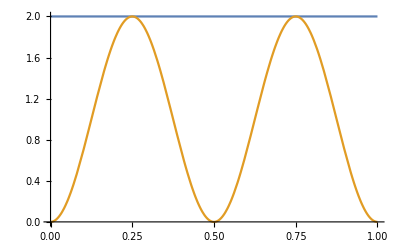

```mathematica
Plot[{densitygs[1,x],densityexc[1,x]},{x,0,1}](* 1 particle, density of the g.s. and 1st excited states *)
```

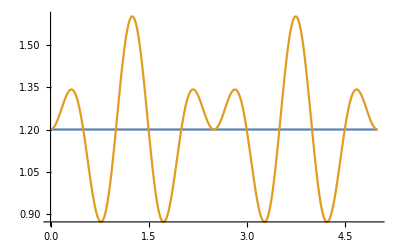

```mathematica
Np=5;Plot[{densitygs[Np,x],densityexc[Np,x]},{x,0,Np}](* 11 particles, density of the g.s. and 1st excited states *)
```

```mathematica
gap=Eexc-Egs//Simplify(* gap energy*)
vs ℏ k[1,L]/.vs->(π ℏ ρ)/m/.L->N/ρ(* energy of a phonon with momentum 2π/L *)
```

(2 π^2 ρ^2 ℏ^2)/(m N)

(2 π^2 ρ^2 ℏ^2)/(m N)